```mathematica
F[y_] := (-(y*0.99/(-1 + y*0.99)))/ 10
F[1.00]
```

9.9

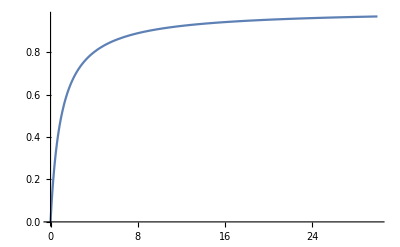

```mathematica
Plot[1 - (1/(x+ 1)), {x, 0, 30}, PlotRange->All]
```

```mathematica
Max: 30 sec?
```

```mathematica
Solve[y== (1 - (1/(x+1))), x]
```

{{x→-y/(-1+y)}}

```mathematica
-1^i            -(-1^i)
```

```mathematica
Tri[i_] := If[EvenQ[i],0, If[Mod[i, 4] == 1,  1/((i)^2), -1/((i)^2)]]
Saw[i_] := 1/i
```

```mathematica
F[i_, a_] :=a Saw[i] + (1-a)Tri[i]
```

```mathematica
G[ a_, x_] := Sum[F[i, a] Sin[i x], {i, 1, 1024}]
```

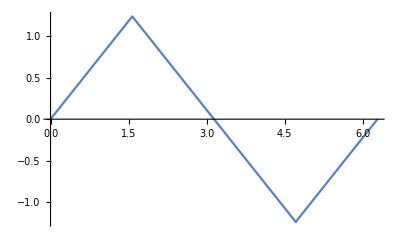

```mathematica
Plot[G[0, x], {x, 0, 2 Pi}]
```

```mathematica
F[4, 2]
```

1/2-π/2